## FeederWatch

```mathematica
raw2017=Import["/Users/katjad/Documents/CitizenScienceData/FeederWatch/PFW_2017_All.csv"];
raw2018=Import["/Users/katjad/Documents/CitizenScienceData/FeederWatch/PFW_2018_All.csv"];
raw2019=Import["/Users/katjad/Documents/CitizenScienceData/FeederWatch/PFW_2019_All.csv"];
raw2020=Import["/Users/katjad/Documents/CitizenScienceData/FeederWatch/PFW_2020_All.csv"];
```

```mathematica
rawGlobal=Join[Rest[#]&/@{raw2017,raw2018,raw2019,raw2020}]
```

$Aborted[]

```mathematica
{{{{"ID","ZiPost","LATITUDE","LONGITUDE","StatProv","ENTRY_TECHNIQUE","FW_Year","Year","Month","Day","PseudoJulian","NHalfDays","EFFORT_HRS_ATLEAST","BirdSpp","NSeen","PlusCode","VALID","REVIEWED","UNUSUAL_SPECIES","SUBMIT_METHOD","LOC_ID","SUB_ID","OBS_ID","SNOW_COV_ATLEAST","SNOW_COV_ATMOST","SNOW_DEP_ATLEAST","SNOW_DEP_ATMOST"},1687365,{"u387607","",33.1225288,-97.1218872,"TX","/GOOGLE_MAP/ZOOM:15","PFW_2017",2017,1,6,67,4,4.001,"brebla",2000,"",1,1,"","","L2423831","S33543945","OBS455602637","","",0.001,4.999}}}, {{{, , , , }}}}
```

```mathematica
GroupBy[#[[8]]/@raw2017]
```

```mathematica
ListLinePlot[Delete[Delete[Delete[Delete[Delete[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(#[[1]][[2]]&)->Last]/@GroupBy[Normal[submitterCountsByWeek],#[[1]][[1]]&],{2}],Range[2017,2020],<||>],{1,-1}],{2,-1}],{3,-1}],{4,-1}],{4,23}],Frame->True,FrameLabel->{"Week","weekly iNaturalist users"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4],PlotRange->All]
```

## Monthly

```mathematica
rawMonthlyFW=Import["/Users/katjad/Documents/CitizenScienceData/FeederWatch/feederwatch.csv"];
```

```mathematica
Grid[rawMonthlyFW,Frame->All]
```

Month | 2017 | 2018 | 2019 | 2020
November | 21022 | 21856 | 24318 | 28490
December | 33533 | 35550 | 36573 | 35343
January | 32039 | 33224 | 34667 | 34969
February | 27945 | 28799 | 30798 | 34932
March | 28738 | 31251 | 33822 | 32983
April | 6306 | 9523 | 3417 | 19152

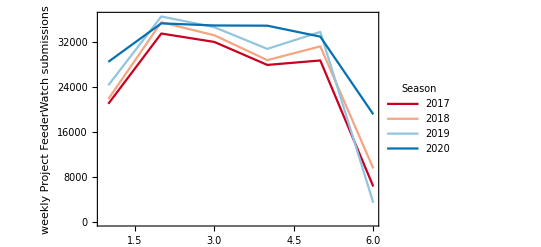

```mathematica
ListLinePlot[Table[Table[rawMonthlyFW[[y]][[x]],{y,2,7}],{x,2,5}],Ticks->{{{1,"Nov"},{2,"Dec"},{3,"Jan"},{4,"Feb"},{5,"Mar"},{6,"Apr"}}, Automatic},Frame->True,FrameLabel->{"","weekly Project FeederWatch submissions"},PlotLegends->LineLegend[{"2017","2018","2019","2020"},LegendLabel->"Season"],PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4],PlotRange->All]
```

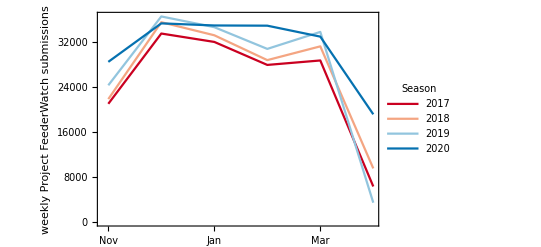

```mathematica
ListLinePlot[Table[Table[rawMonthlyFW[[y]][[x]],{y,2,7}],{x,2,5}],FrameTicks->{Automatic,{{{1,"Nov"},{2,"Dec"},{3,"Jan"},{4,"Feb"},{5,"Mar"},{6,"Apr"}},None}},FrameLabel->{"","weekly Project FeederWatch submissions"},Frame->True,PlotLegends->LineLegend[{"2017","2018","2019","2020"},LegendLabel->"Season"],PlotTheme->"LargeLabels",PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4],PlotRange->All]
```